# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Quantum channel/MAC Computations/QMB.wl"];
Get["/Users/pcs/Desktop/Quantum channel/MAC Computations/EntanglementWorkflow3.wl"];
```

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Chop[Total[Map[VNentropy,Chop[Eigenvalues[rho]]]]]
];
(*Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];*)
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]]+I RandomVariate[NormalDistribution[0,1]],{2^L}]];
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Tr[Chop[rho.rho]]
];
(*Compute total decoherence via trapezoidal rule*)
decoherence[purity_,tlist_]:=Module[{pur=Chop[purity]},(1/tlist[[-1]])Total[Table[(pur[[i]]+pur[[i+1]])/2*(tlist[[i+1]]-tlist[[i]]),{i,1,Length[purity]-1}]]]
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

# Ising scatter plots

```mathematica
J=1;
h=1.05;
L=6;
g=2.5;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
Ha=IsingHamiltonian[1,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=1;
Lb=L-La;
sdiageigenvec=ParallelTable[sdiag[L,La,Lb,i],{i,allvecs},DistributedContexts->Full];
```

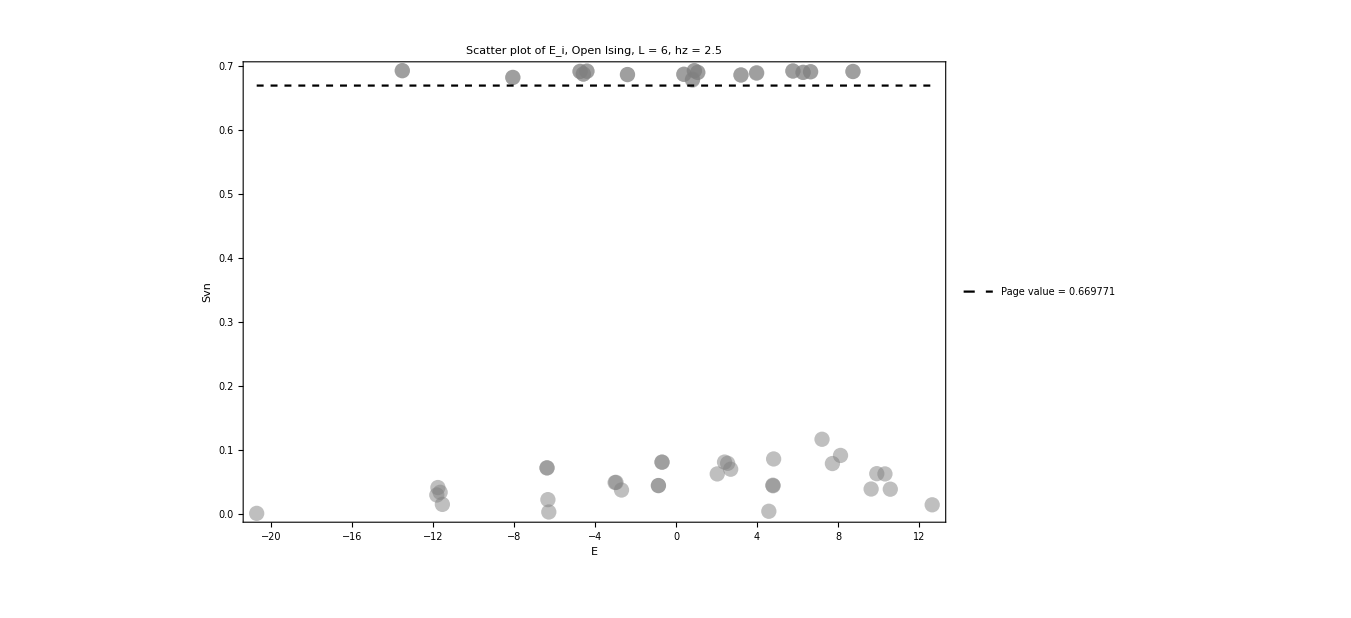

```mathematica
Show[{ListPlot[Transpose[{allvals,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Open Ising, L = "<>ToString[L]<>", hz = "<>ToString[g]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[allvals],Max[allvals]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

```mathematica
productstate2=Table[RandomChainProductState[L],50];
(*productstate2=Table[Flatten[KroneckerProduct[haar[1],haar[L-1]]],50];*)
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].Ha.i],{i,productstate2},DistributedContexts->Full];
```

```mathematica
data=SortBy[Transpose[{iprs,energies,productstate2}],First];
productstate=data[[1;;5]][[All,3]];
```

```mathematica
tlist=Table[i,{i,0,200,0.05}];
tlist//Length
```

4001

```mathematica
fakesvn=Table[ParallelTable[{t,svn[L,La,Lb,i,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

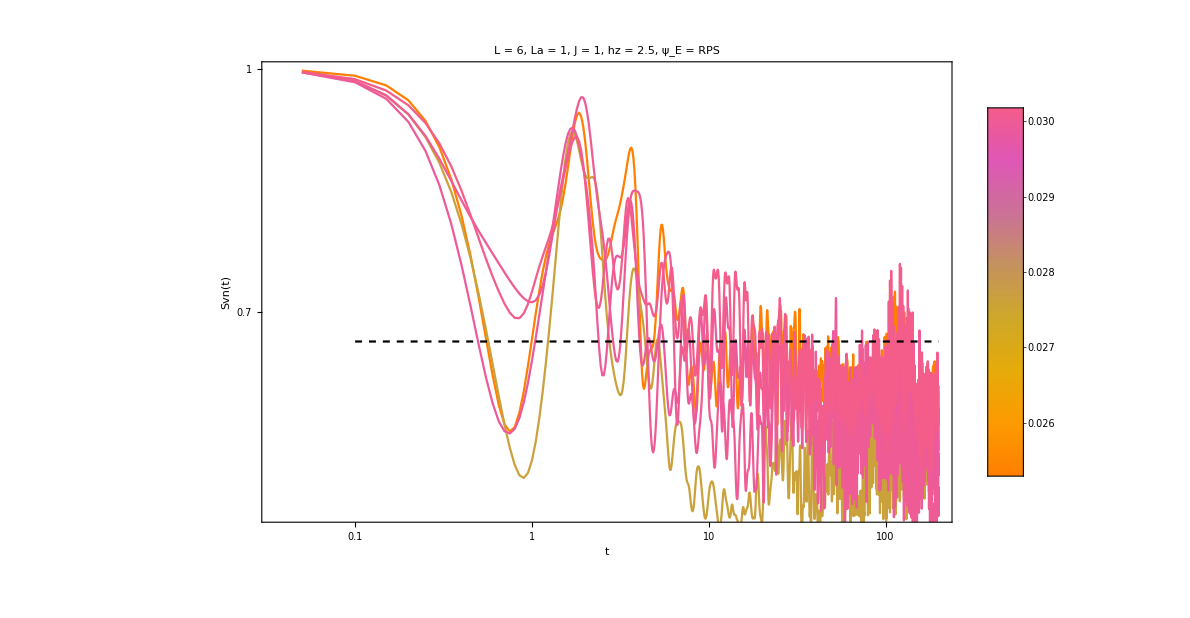

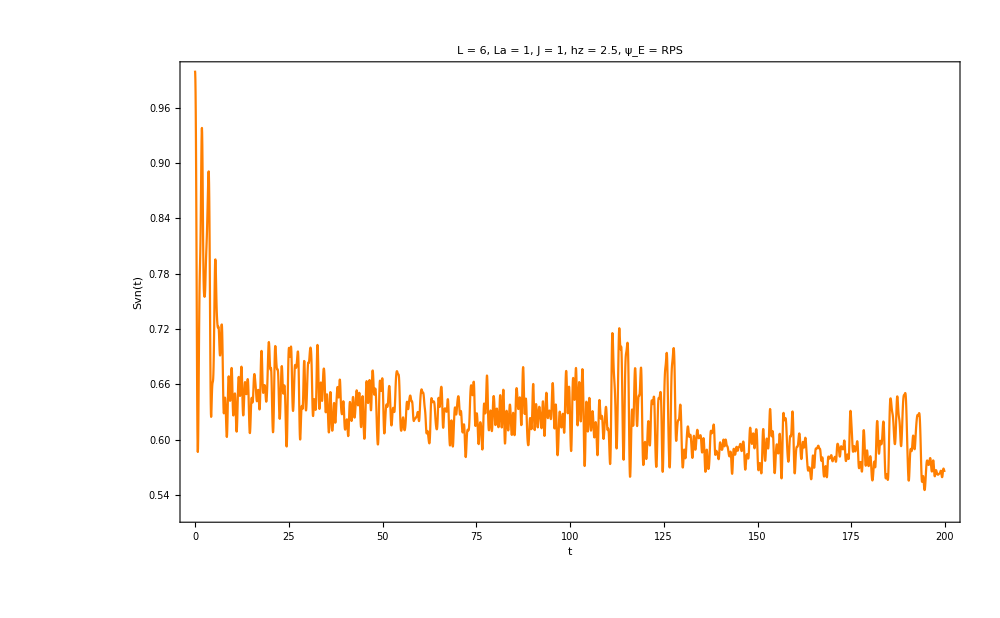

```mathematica
(*Step 1:Determine the overall energy range*)
sorted=data[[1;;5]][[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
(*Step 2:Define a function to map an energy value to a temperature-like color*)
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListLogLogPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}];
Legended[Show[{plots,LogLogPlot[pageEntropy[La,Lb],{x,10^-1,Max[tlist]},PlotStyle->{Directive[Black,Dashed]}]}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
i=1;
ListPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]]
```

# Choi matrix ising

## Test

```mathematica
i=1;
ψ=productstate[[i]];
rho=Chop[MatrixPartialTrace[Dyad[ψ],1,{2^La,2^Lb}]];
```

```mathematica
{L,La,Lb}
ψ//Dimensions
rho//Dimensions
```

{6,1,5}

{64}

{32,32}

```mathematica
A=KroneckerProduct[IdentityMatrix[2^(Lb)]/2^(La),rho];
P=Transpose[allvecs];
Pinv=Conjugate[allvecs];
```

```mathematica
A//Dimensions
allvecs//Dimensions
```

{1024,1024}

{64,64}

```mathematica
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*allvals*t]].Pinv;
```

```mathematica
AbsoluteTiming[chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist}];
truepurity=Chop[Map[Tr,Map[#.#&,chois]]];]
```

{62.1557,Null}

```mathematica
chois[[1]]//Dimensions
```

{4,4}

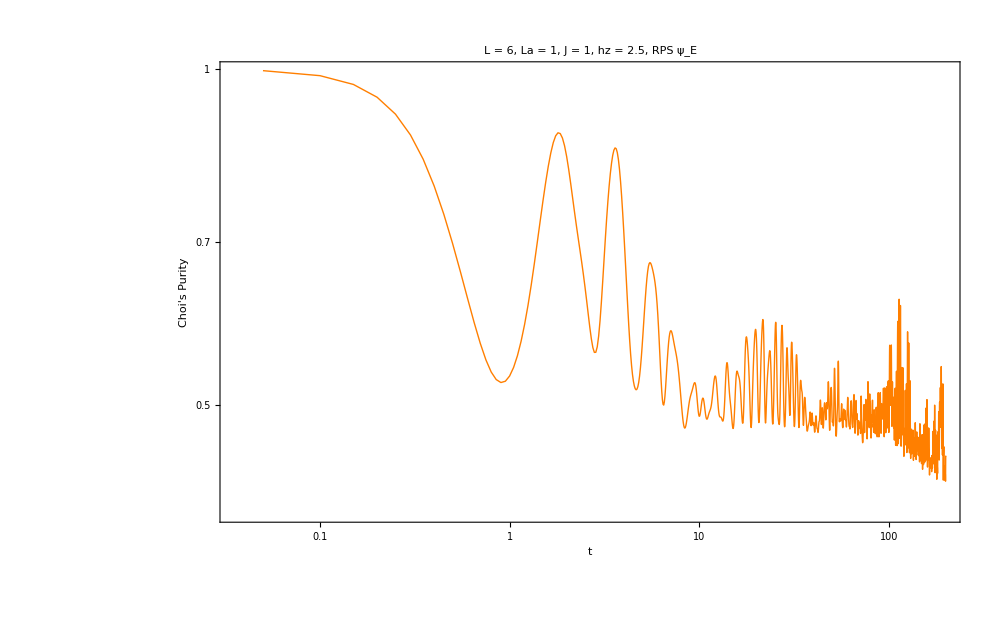

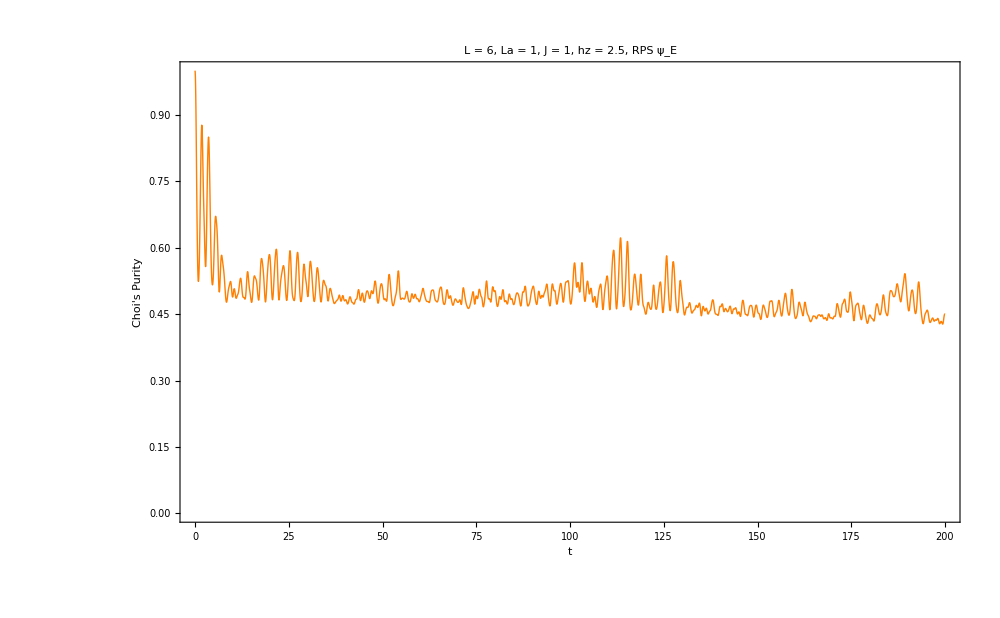

0.492738

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,truepurity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]],Thick]];
final=Show[{plot,LogLogPlot[1/((2^La)^2),{x,10^-1,tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}]
ListPlot[Transpose[{tlist,truepurity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]],Thick]]
decoherence[truepurity,tlist]
```

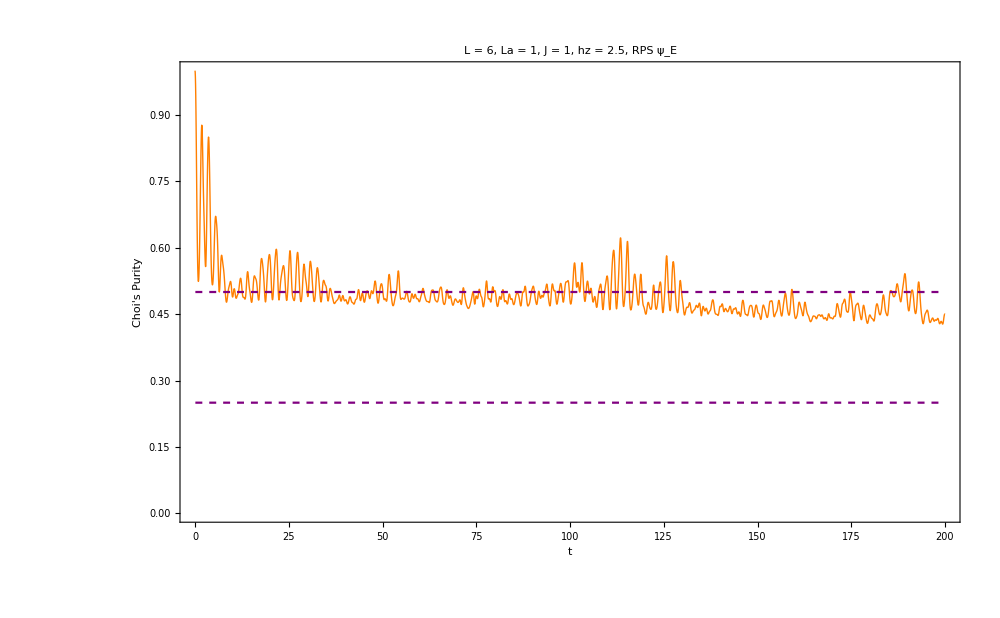

```mathematica
plot=ListPlot[Transpose[{tlist,truepurity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]],Thick]];
Show[{plot,Plot[{0.5,0.25},{x,10^-1,tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}]
```

## Cycle ψ_E

```mathematica
parameters=Flatten[Table[{i,j},{i,0,2,0.2},{j,0,2,0.2}],1];
parameters//Length
```

121

```mathematica
hx=Range[0,2,0.1];
hz=Range[0,1,0.1];
```

```mathematica
data={};
Do[

Ha=IsingHamiltonian[i[[1]],i[[2]],1,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
P=Transpose[allvecs];
Pinv=Conjugate[allvecs];
U[t_]:=P.DiagonalMatrix[Exp[-I*allvals*t]].Pinv;
chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist}];
purity=Chop[Map[Tr,Map[#.#&,chois]]];

AppendTo[data,{i[[1]],i[[2]],decoherence[purity,tlist]}];
,{i,parameters}];
```

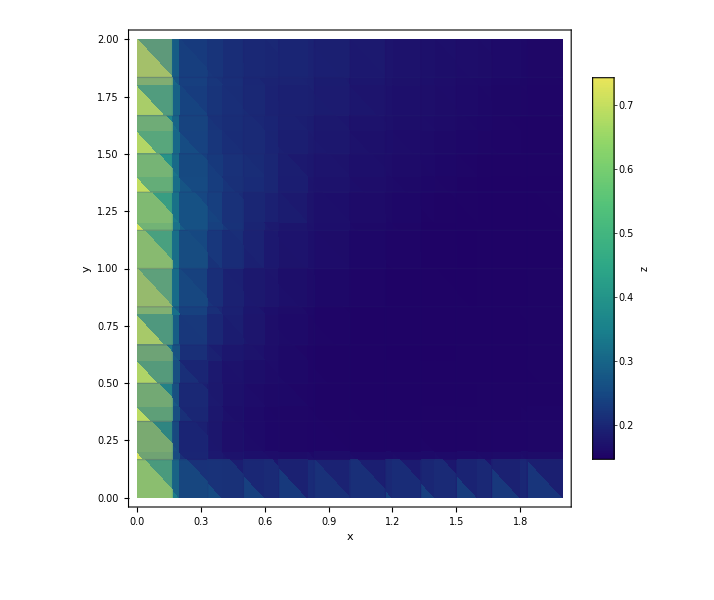

```mathematica
(*assuming `data` is the {{x,y,z},...} list shown*)xs=Sort@DeleteDuplicates[data[[All,1]]];
ys=Sort@DeleteDuplicates[data[[All,2]]];
{zmin,zmax}=MinMax[data[[All,3]]];

ldp=ListDensityPlot[data,(*smooth but not overdone*)ColorFunction->"BlueGreenYellow",(*uniform scientific palette*)ColorFunctionScaling->True,PlotRange->{zmin,zmax},Frame->True,FrameLabel->(Style[#,16]&/@{"x","y"}),AspectRatio->1,ImageSize->600,PlotLegends->BarLegend[{"BlueGreenYellow",{zmin,zmax}},LabelStyle->14,LegendLabel->Style["z",14]],Mesh->{Length[xs],Length[ys]},MeshStyle->Directive[White,Opacity[.2]],PlotTheme->"Detailed",Ticks->{Table[{x,x},{x,xs}],Table[{y,y},{y,ys}]}];
ldp
```

## Slow code via krauss code

```mathematica
(*Dimensions*)
dA=2^La;  (*system size*)
dB=2^Lb;  (*environment size*)
(*Maximally entangled projector on A'⊗A*)
vecPhi=Flatten[IdentityMatrix[dA]]/Sqrt[dA];       (* |Φ+>as a vector*)
Phi=Outer[Times,vecPhi,Conjugate[vecPhi]];    (* |Φ+><Φ+|*)
(*Big unitary:I_{A'}⊗U_{AE}(t)*)
Clear[Ubig];
Ubig[t_]:=KroneckerProduct[IdentityMatrix[dA],U[t]];
(*Partial trace over the environment E (the last factor of AE after evolution).We reshape to A' (dA),A_out (dA),E_out (dB) on bra/ket and contract E.*)
Clear[PartialTraceEnv];
PartialTraceEnv[X_?MatrixQ]:=Module[{T,Y},T=ArrayReshape[X,{dA,dA,dB,dA,dA,dB}];
Y=TensorContract[T,{{3,6}}];(*trace over E indices*)ArrayReshape[Y,{dA*dA,dA*dA}]];
(*Choi state of the reduced channel at time t (trace=1 by construction)*)
Clear[ChoiState];
ChoiState[t_]:=Module[{X},X=Ubig[t].KroneckerProduct[Phi,Transpose[rho]].ConjugateTranspose[Ubig[t]];
Chop@PartialTraceEnv[X]];
(*Purity (no extra normalization needed;Tr[J]==1)*)
Clear[ChoiPurityAt];
ChoiPurityAt[t_]:=Module[{J=ChoiState[t]},Tr[J.J]//Chop];
```

```mathematica
J0=ChoiState[0];
{Tr[J0],Tr[J0.J0]}//Chop
```

{1.,1.}

```mathematica
purity=ParallelMap[ChoiPurityAt,tlist,DistributedContexts->Full];
purity[[1;;20]]
```

{0.98083,0.980744,0.980658,0.980571,0.980483,0.980396,0.980308,0.980219,0.98013,0.980041,0.979951,0.979861,0.979771,0.97968,0.979589,0.979497,0.979405,0.979312,0.97922,0.979126}

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[Black,Dashed]];
finalb=Show[{plot,LogLogPlot[1/((2^La)^2),{x,10^-1,tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}];
```

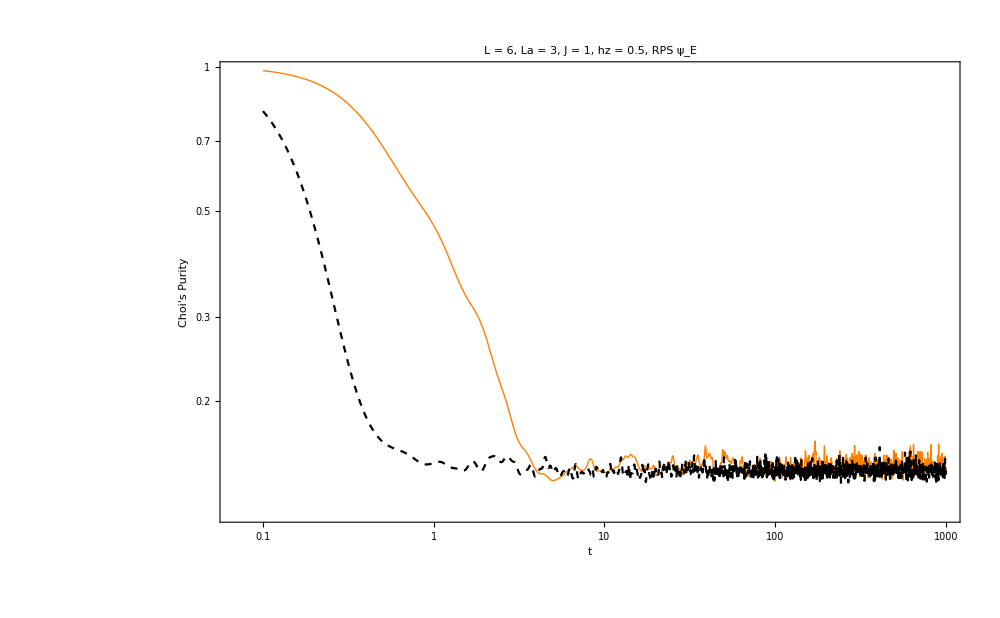

```mathematica
Show[{final,finalb}]
```

## Improved code (equal size bipartitions)

```mathematica
ClearAll[reshuffle]
reshuffle[a_,m_,n_]:=Module[{reshaped},reshaped=ArrayReshape[a,{m,n,m,n}];
ArrayReshape[Transpose[reshaped,{1,3,2,4}],{m*n,m*n}]];
```

```mathematica
{L,La,Lb}
```

{6,3,3}

```mathematica
(*assumes psi,la,lb are already defined*)
m=2^La;
n=2^Lb;
rho=MatrixPartialTrace[Dyad[ψ],1,{m,n}]//Chop;
id=IdentityMatrix[n]/m;
a=KroneckerProduct[id,rho];
```

```mathematica
ψ//Dimensions
rho//Dimensions
id//Dimensions
a//Dimensions
```

{64}

{8,8}

{8,8}

{64,64}

```mathematica
unitary[t_]:=Transpose[allvecs].DiagonalMatrix[Exp[-I*allvals*t]].Conjugate[allvecs];
```

```mathematica
ClearAll[reshuffledUnitary];
reshuffledUnitary[t_]:=reshuffle[unitary[t],m,n];
```

```mathematica
choiMatrixFast[t_]:=Module[{ur},ur=reshuffledUnitary[t];
ur.a.ConjugateTranspose[ur]//Chop];
```

```mathematica
AbsoluteTiming[purity=ParallelMap[Chop[Tr[#.#]&@*choiMatrixFast],tlist];]
```

{0.90182,Null}

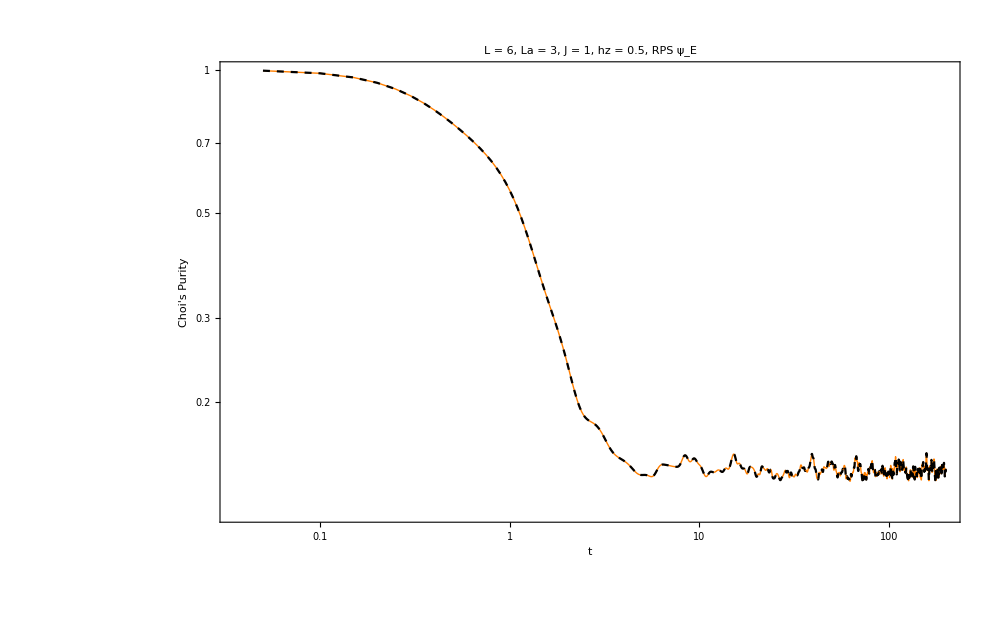

0.148104

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[Black,Dashed]];
finalb=Show[{plot,LogLogPlot[1/((2^La)^2),{x,10^-1,tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}];
Show[{final,finalb}]
decoherence[purity,tlist]
```

## improved Cycle ψ_E (equal size bipartitions)

```mathematica
parameters=Flatten[Table[{i,j},{i,0,3,0.1},{j,0,3,0.1}],1];
parameters//Length
```

961

```mathematica
data={};
Do[

Ha=IsingHamiltonian[1,i[[1]],i[[2]],L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];


unitary[t_]:=Transpose[allvecs].DiagonalMatrix[Exp[-I*allvals*t]].Conjugate[allvecs];
reshuffledUnitary[t_]:=reshuffle[unitary[t],m,n];
choiMatrixFast[t_]:=Module[{ur},ur=reshuffledUnitary[t];
Chop[ur.a.ConjugateTranspose[ur]]];
purity=ParallelMap[Chop[Tr[#.#]&@*choiMatrixFast],tlist];

AppendTo[data,{i[[1]],i[[2]],decoherence[purity,tlist]}];
,{i,parameters}];
(*Export["test_fullmesh_ising_choipurity.m",data]*)
```

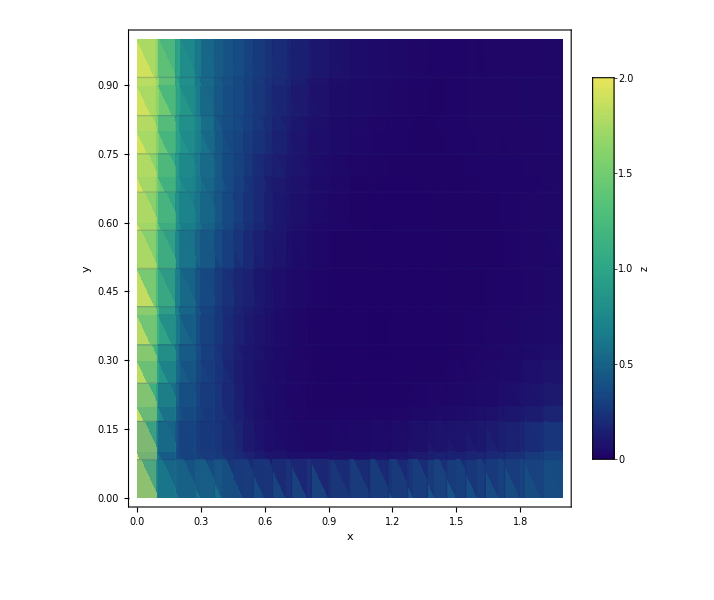

```mathematica
(*assuming `data` is the {{x,y,z},...} list shown*)
xs=Sort@DeleteDuplicates[Chop[data[[All,1]]]];
ys=Sort@DeleteDuplicates[Chop[data[[All,2]]]];
{zmin,zmax}=MinMax[Chop[data]];

ldp=ListDensityPlot[Chop[data],(*smooth but not overdone*)ColorFunction->"BlueGreenYellow",(*uniform scientific palette*)ColorFunctionScaling->True,PlotRange->{zmin,zmax},Frame->True,FrameLabel->(Style[#,16]&/@{"x","y"}),AspectRatio->1,ImageSize->600,PlotLegends->BarLegend[{"BlueGreenYellow",{zmin,zmax}},LabelStyle->14,LegendLabel->Style["z",14]],Mesh->{Length[xs],Length[ys]},MeshStyle->Directive[White,Opacity[.2]],PlotTheme->"Detailed",Ticks->{Table[{x,x},{x,xs}],Table[{y,y},{y,ys}]}];
ldp
```

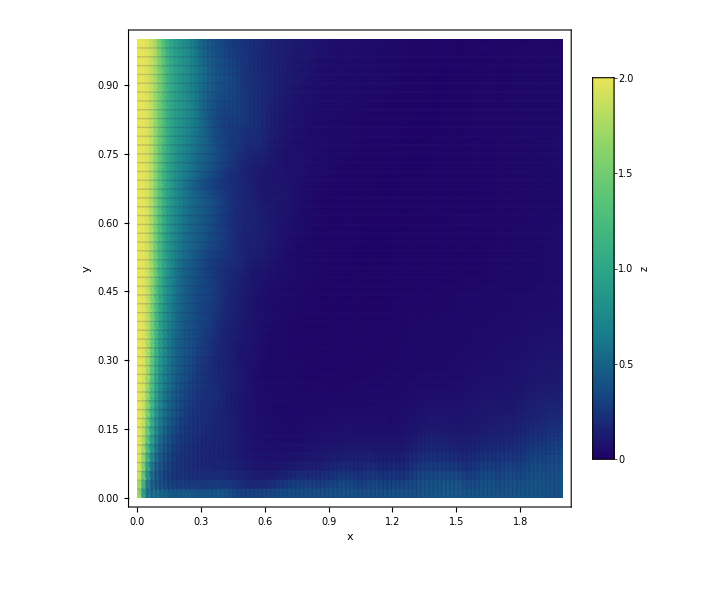

```mathematica
(*assuming `data` is the {{x,y,z},...} list shown*)
xs=Sort@DeleteDuplicates[Chop[data[[All,1]]]];
ys=Sort@DeleteDuplicates[Chop[data[[All,2]]]];
{zmin,zmax}=MinMax[Chop[data]];

ldp=ListDensityPlot[Chop[data],(*smooth but not overdone*)ColorFunction->"BlueGreenYellow",(*uniform scientific palette*)ColorFunctionScaling->True,PlotRange->{zmin,zmax},Frame->True,FrameLabel->(Style[#,16]&/@{"x","y"}),AspectRatio->1,ImageSize->600,PlotLegends->BarLegend[{"BlueGreenYellow",{zmin,zmax}},LabelStyle->14,LegendLabel->Style["z",14]],Mesh->{Length[xs],Length[ys]},MeshStyle->Directive[White,Opacity[.2]],PlotTheme->"Detailed",Ticks->{Table[{x,x},{x,xs}],Table[{y,y},{y,ys}]}];
ldp
```

```mathematica
newdata=Table[{data[[i,1]],data[[i,2]],1-data[[i,3]]},{i,Length[data]}];
```

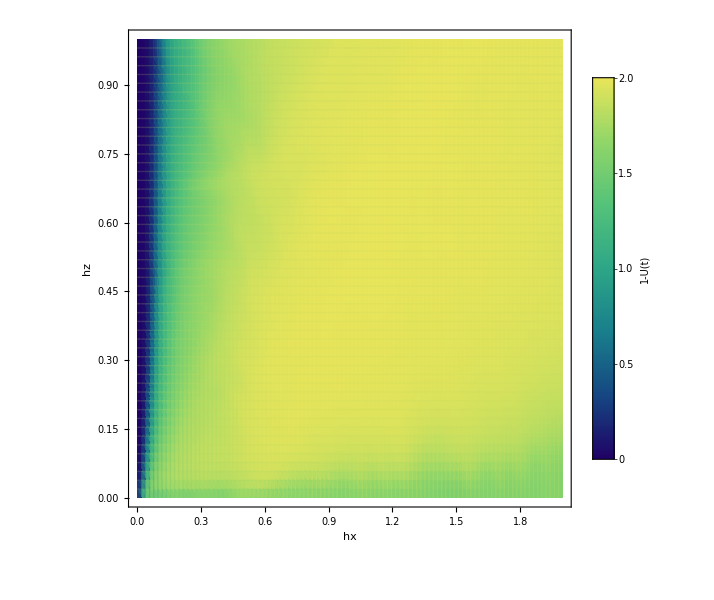

```mathematica
(*assuming `data` is the {{x,y,z},...} list shown*)
xs=Sort@DeleteDuplicates[Chop[newdata[[All,1]]]];
ys=Sort@DeleteDuplicates[Chop[newdata[[All,2]]]];
{zmin,zmax}=MinMax[Chop[newdata]];

ldp=ListDensityPlot[Chop[newdata],(*smooth but not overdone*)ColorFunction->"BlueGreenYellow",(*uniform scientific palette*)ColorFunctionScaling->True,PlotRange->{zmin,zmax},Frame->True,FrameLabel->(Style[#,25]&/@{"hx","hz"}),FrameStyle->Directive[Black,20],AspectRatio->1,ImageSize->600,PlotLegends->BarLegend[{"BlueGreenYellow",{zmin,zmax}},LabelStyle->14,LegendLabel->Style["1-U(t)",20]],Mesh->{Length[xs],Length[ys]},MeshStyle->Directive[White,Opacity[.2]],PlotTheme->"Detailed",Ticks->{Table[{x,x},{x,xs}],Table[{y,y},{y,ys}]}];
ldp
```

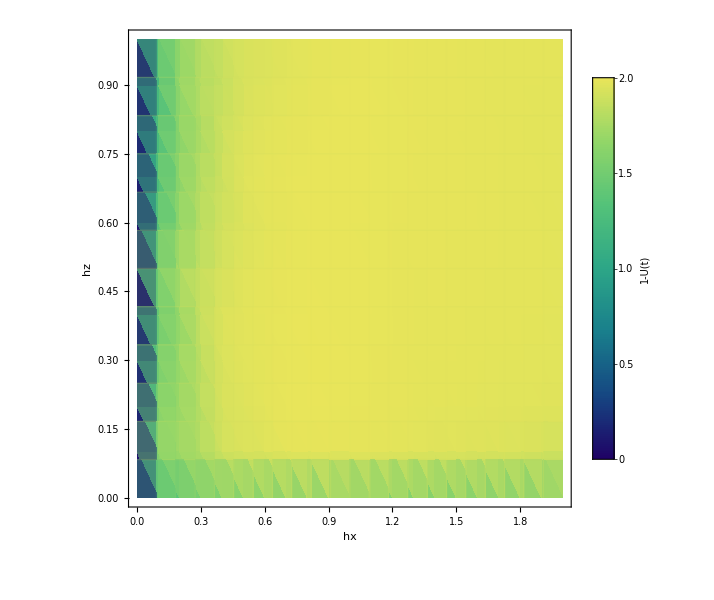

```mathematica
newdata=Table[{data[[i,1]],data[[i,2]],1-data[[i,3]]},{i,Length[data]}];
(*assuming `data` is the {{x,y,z},...} list shown*)
xs=Sort@DeleteDuplicates[Chop[newdata[[All,1]]]];
ys=Sort@DeleteDuplicates[Chop[newdata[[All,2]]]];
{zmin,zmax}=MinMax[Chop[newdata]];

ldp=ListDensityPlot[Chop[newdata],(*smooth but not overdone*)ColorFunction->"BlueGreenYellow",(*uniform scientific palette*)ColorFunctionScaling->True,PlotRange->{zmin,zmax},Frame->True,FrameLabel->(Style[#,25]&/@{"hx","hz"}),FrameStyle->Directive[Black,20],AspectRatio->1,ImageSize->600,PlotLegends->BarLegend[{"BlueGreenYellow",{zmin,zmax}},LabelStyle->14,LegendLabel->Style["1-U(t)",20]],Mesh->{Length[xs],Length[ys]},MeshStyle->Directive[White,Opacity[.2]],PlotTheme->"Detailed",Ticks->{Table[{x,x},{x,xs}],Table[{y,y},{y,ys}]}];
ldp
```

## Improved code B

```mathematica
(*plot=ListLogLogPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[Black,Dashed]];
finalb=Show[{plot,LogLogPlot[1/((2^La)^2),{x,10^-1,tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}];
Show[{final,finalb}]
decoherence[purity,tlist]*)
```

```mathematica
(*system/env sizes*)
m=2^La;
n=2^Lb;
d=m n;
Needs["Developer`"];
(*environment state ρ_E (n×n)*)
rhoE=Developer`ToPackedArray@Chop@MatrixPartialTrace[Dyad[ψ],1,{m,n}];
(*spectral unitary:scale columns (faster than DiagonalMatrix every t)*)
P=Developer`ToPackedArray@Transpose[allvecs];
Pinv=Developer`ToPackedArray@Conjugate[allvecs];
unitary[t_]:=Module[{ph=Developer`ToPackedArray@Exp[-I allvals t]},With[{Pph=Transpose[Transpose[P]*ph]},Developer`ToPackedArray@(Pph.Pinv)]];
(*maximally entangled|Φ_m⟩ on reference R and input S*)
phi=Developer`ToPackedArray@(Flatten[IdentityMatrix[m]]/Sqrt[m]);  (*length m^2*)
projPhi=Developer`ToPackedArray@Dyad[phi];                          (*m^2×m^2*)
(*Choi of the reduced channel on the SYSTEM (size m^2×m^2)*)
choiSys[t_]:=Module[{U=unitary[t],UR,Omega,X},UR=KroneckerProduct[IdentityMatrix[m,SparseArray],U];(*acts on R⊗S⊗E*)Omega=KroneckerProduct[projPhi,rhoE];(* |Φ⟩⟨Φ|⊗ρ_E*)X=UR.Omega.ConjugateTranspose[UR];
Developer`ToPackedArray@Chop@MatrixPartialTrace[X,3,{m,m,n}]  (*trace E*)];
```

```mathematica
choiSys[0.]//Dimensions
```

{4,4}

```mathematica
(*your purity:Tr[J^2] on m^2×m^2 (for m=2 this is 4×4)*)
AbsoluteTiming[purity=ParallelMap[(Chop@Re@Tr[#.#])&@*choiSys,tlist];]
```

{2.22748,Null}

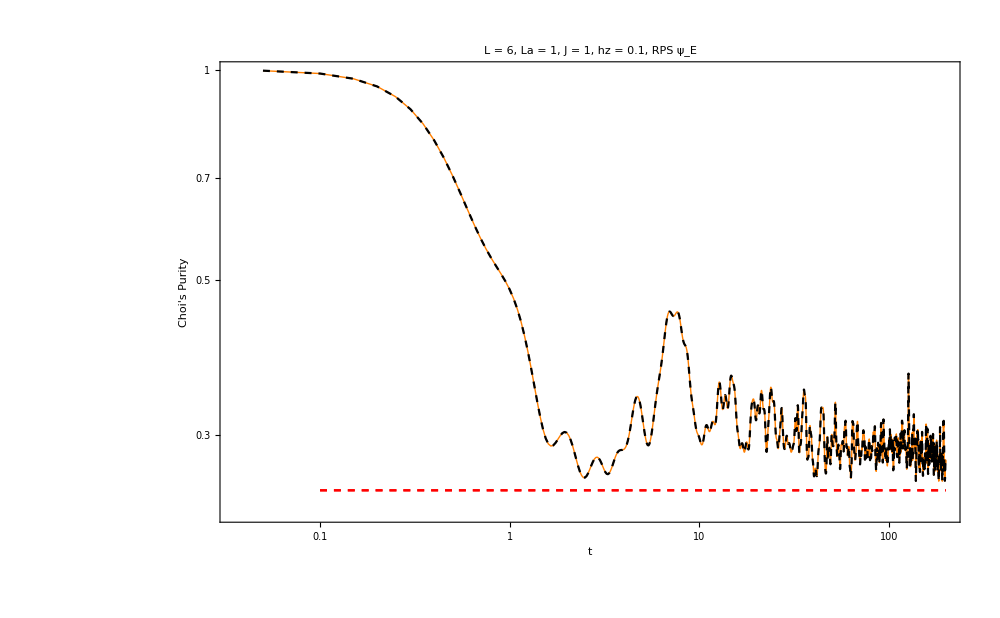

0.294877

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[Black,Dashed]];
finalb=Show[{plot,LogLogPlot[1/((2^La)^2),{x,10^-1,tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}];
Show[{final,finalb}]
decoherence[purity,tlist]
```

## Improved code c

```mathematica
(* ============================*)(*Reusable channel utilities*)(* ============================*)
Needs["Developer`"];
(*0) Helpers*)
ClearAll[PackC];
PackC[x_]:=Developer`ToPackedArray[x];
(*1) Environment state from a global pure state|ψ⟩ on S⊗E*)
ClearAll[EnvStateFromPsi];
EnvStateFromPsi[psi_,m_Integer?Positive,n_Integer?Positive]:=PackC@Chop@MatrixPartialTrace[Dyad[psi],1,{m,n}];
(*2) Fast spectral unitary builder:U(t)=V.diag(e^{-i λ t}).V^†,implemented via column scaling (no DiagonalMatrix allocation)*)
ClearAll[SpectralUnitary];
SpectralUnitary[allvecs_,allvals_]:=Module[{P=PackC@Transpose[allvecs],Pinv=PackC@Conjugate[allvecs]},Function[{t},With[{ph=PackC@Exp[-I allvals t]},PackC@(Transpose[Transpose[P]*ph].Pinv)]]];
(*3) Maximally entangled projector on R⊗S (dimension m)*)
ClearAll[PhiProjector];
PhiProjector[m_Integer?Positive]:=Module[{phi=PackC@(Flatten[IdentityMatrix[m]]/Sqrt[m])},PackC@Dyad[phi]               (*m^2×m^2*)];
(*4) Choi of reduced system channel via ancilla definition.Inputs:-m,n (system/env dims)-unitaryF[t_] (Function returning U(t) on S⊗E)-rhoE (n×n) OR psi (mn-vector)[set exactly one] Returns a Function[{t},J(t)] with J(t) size m^2×m^2.*)
ClearAll[ChoiSysBuilder];
Options[ChoiSysBuilder]={"rhoE"->None,"psi"->None};
ChoiSysBuilder[m_Integer?Positive,n_Integer?Positive,unitaryF_Function,opts:OptionsPattern[]]:=Module[{rhoE=OptionValue["rhoE"],psi=OptionValue["psi"],projPhi,idm},If[rhoE===None&&psi===None,Message[ChoiSysBuilder::envspec];Return[$Failed]];
If[rhoE=!=None&&psi=!=None,Message[ChoiSysBuilder::envboth];Return[$Failed]];
rhoE=If[rhoE===None,EnvStateFromPsi[psi,m,n],rhoE]//PackC;
projPhi=PhiProjector[m];
idm=IdentityMatrix[m,SparseArray];(*sparse identity*)Function[{t},Module[{U=unitaryF[t],UR,Omega,X},UR=KroneckerProduct[idm,U];(*acts on R⊗S⊗E*)Omega=KroneckerProduct[projPhi,rhoE];(* |Φ⟩⟨Φ|⊗ρE*)X=UR.Omega.ConjugateTranspose[UR];
PackC@Chop@MatrixPartialTrace[X,3,{m,m,n}]  (*trace E,keep R⊗S_out*)]]];
ChoiSysBuilder::envspec="Provide either \"rhoE\" -> (n×n matrix) or \"psi\" -> (mn-vector).";
ChoiSysBuilder::envboth="Provide only one of \"rhoE\" or \"psi\", not both.";
(*5) Process-purity from a Choi function:Tr[J(t)^2]*)
ClearAll[ProcessPurity];
Options[ProcessPurity]={"Parallel"->True};
ProcessPurity[choiF_Function,tlist_List,OptionsPattern[]]:=Module[{par=TrueQ[OptionValue["Parallel"]]},If[par,ParallelMap[(Chop@Re@Tr[#.#])&@*choiF,tlist,Method->"CoarsestGrained"],Map[(Chop@Re@Tr[#.#])&@*choiF,tlist]]];
```

```mathematica
(*Problem-specific sizes*)
m=2^La;
n=2^Lb;
(*Option A:environment given as a pure global state|ψ⟩*)
rhoE=EnvStateFromPsi[ψ,m,n];
(*Build U(t) from your spectrum*)
unitaryF=SpectralUnitary[allvecs,allvals];
(*Build Choi[J](t) for the system channel*)
choiF=ChoiSysBuilder[m,n,unitaryF,"rhoE"->rhoE];
```

```mathematica
(*Purity over your tlist*)
AbsoluteTiming[purity=ProcessPurity[choiF,tlist];]
```

{2.43632,Null}

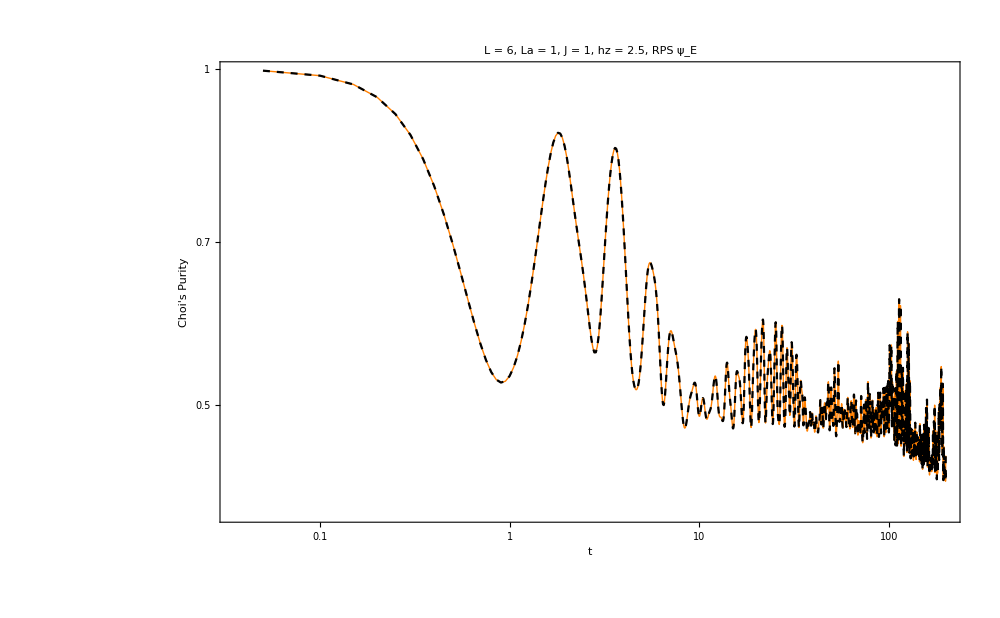

0.492738

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[Black,Dashed]];
finalb=Show[{plot,LogLogPlot[1/((2^La)^2),{x,10^-1,tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}];
Show[{final,finalb}]
decoherence[purity,tlist]
```

## improved Cycle ψ_E

```mathematica
parameters=Flatten[Table[{i,j},{i,0,3,0.1},{j,0,3,0.1}],1];
parameters//Length
```

961

```mathematica
data={};
Do[

Ha=IsingHamiltonian[1,i[[1]],i[[2]],L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];

(*Build U(t) from your spectrum*)
unitaryF=SpectralUnitary[allvecs,allvals];
(*Build Choi[J](t) for the system channel*)
choiF=ChoiSysBuilder[m,n,unitaryF,"rhoE"->rhoE];
(*Purity over your tlist*)
purity=ProcessPurity[choiF,tlist];

AppendTo[data,{i[[1]],i[[2]],decoherence[purity,tlist]}];
,{i,parameters}];
Export["test_fullmesh_ising_choipurity_JA.m",data]
```

test_fullmesh_ising_choipurity_JA.m

```mathematica
newdata=Table[{data[[i,1]],data[[i,2]],1-data[[i,3]]},{i,Length[data]}];
```

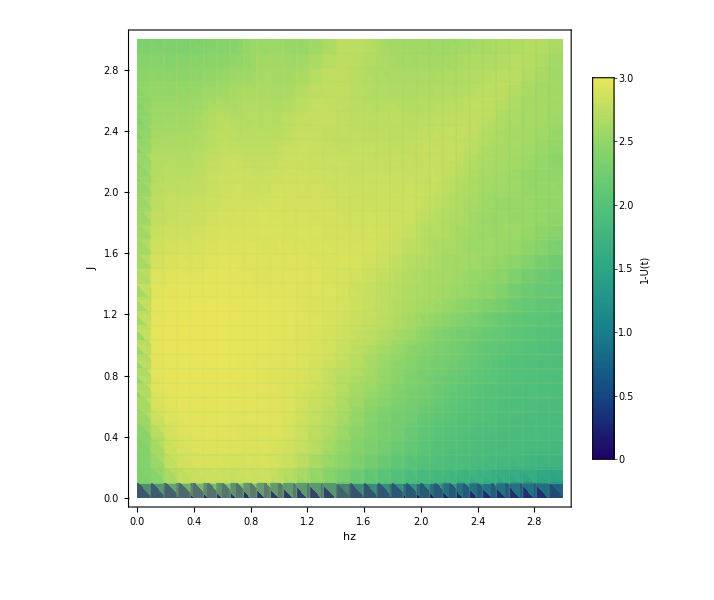

```mathematica
(*assuming `data` is the {{x,y,z},...} list shown*)
xs=Sort@DeleteDuplicates[Chop[newdata[[All,1]]]];
ys=Sort@DeleteDuplicates[Chop[newdata[[All,2]]]];
{zmin,zmax}=MinMax[Chop[newdata]];

ldp=ListDensityPlot[Chop[newdata],(*smooth but not overdone*)ColorFunction->"BlueGreenYellow",(*uniform scientific palette*)ColorFunctionScaling->True,PlotRange->{zmin,zmax},Frame->True,FrameLabel->(Style[#,25]&/@{"hz","J"}),FrameStyle->Directive[Black,20],AspectRatio->1,ImageSize->600,PlotLegends->BarLegend[{"BlueGreenYellow",{zmin,zmax}},LabelStyle->14,LegendLabel->Style["1-U(t)",20]],Mesh->{Length[xs],Length[ys]},MeshStyle->Directive[White,Opacity[.2]],PlotTheme->"Detailed",Ticks->{Table[{x,x},{x,xs}],Table[{y,y},{y,ys}]}];
ldp
```